```mathematica
(*spin_rotation_angle_20250115: attempt to add garnet and contaminant magnetizations before determining Tc*)(*spin_rotation_angle_20250109: total magnetization reverted to conventional signs - below Tc, M > 0; adjusted contaminants accordingly; study various field coefficient dependence*)
(*spin_rotation_angle_20241030: Molecular field calculation added to notebook*)
(*spin_rotation_angle_20241025_2: Total magnetization negated to match direction taken as positive*)
(*spin_rotation_angle_20241025: added perovskite and hematite contributions*)
(*spin_rotation_angle_20240920: sample geometry matches 2024 arXiv preprint*)
```

gamma                          = 0.32

Jc''                           = 3.96

gc''                           = 1.75758

gcs''                          = 1.51515

Tc (K)                         = 266.18

contribution of Tb at Tc (uB)  = 3.9522

spin component at Tc (uB)      = 3.40707

contribution of 2Fe at Tc (uB) = 9.27286

contribution of 3Fe at Tc (uB) = -13.2251

spin excess at Tc (uB)         = -0.54513

M at 256.18 K = 0.130466 uB/molecule

M at 266.18 K = 3.29018×10^-16 uB/molecule

M at 276.18 K = -0.117276 uB/molecule

M at 296. K = -0.315298 uB/molecule

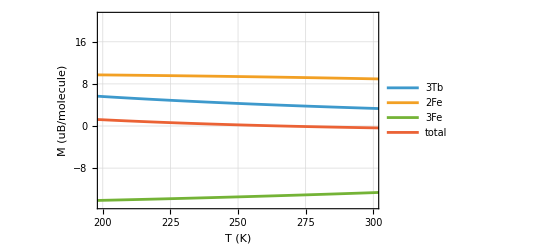

```mathematica
(*Magnetization from molecular field theory*)
Clear[dT,Tm,NA,muB,rho,A,kB,h,naa,nad,ndd,nac,ncc,ndd,Jc,Sc,Lc,Ja,Sa,La,Jd,Sd,Ld,gamma,Lcpp,Jcpp,d,gc,gcs,ga,gd,gcpp,muc0,mua0,mud0,xc,xa,xd,bjc,bja,bjd,rtr,n,muct,muat,mudt,must,i,tc,muctc,muatc,mudtc,sctc,sxtc,mutp,musti,imust,mustp,imustp,Treq,lTreq,Mreq,mutp];

(*input*)
(*Temperature parameters*)
dT=1.;   (*increment, K*)
Tm=400;  (*maximum, K*)

(*physical constants*)
NA=6.02 10^23;(*Avogadro*)
muB=9.274 10^-21;(*Bohr magneton,erg/G*)
kB=1.381 10^-16 ;(*Boltzmann, erg/K*)

(*field coefficients in mol/cc*)
naa=-65.0;  (*octahedral-octahedral[Dionne71]*)
nad=97.0;     (*octahedral-tetrahedral[Dionne71]*)
ndd=-30.4;(*tetrahedral-tetrahedral[Dionne71]*)

nac=-4.2 ;(*octahedral-dodecahedral[Dionne79, Dionne09]*)
ncc=0.;   (*dodecahedral-dodecahedral[Dionne79, Dionne09]*)
ncd=6.5;  (*dodecahedral-tetrahedral[Dionne79, Dionne09]*)

(*
naa=-51;(*new best fit to HFIR*)
nad=82.3;(*new best fit to HFIR*)
ndd=-33;(*new best fit to HFIR*)

nac=-3;(*new best fit to HFIR*)
ncc=0.;   (*new best fit to HFIR*)
ncd=5;  (*new best fit to HFIR*)
*)

(*angular momenta in hbar[Dionne09]*)
gamma=0.32; (*quenching factor*)

(*gamma=0.25;(*quenching factor to yield Tc = 250 K, empirical*)*)
Sc=3;(*Tb spin*)
Lc=gamma 3;(*Tb orbit*)
Jc=Lc+Sc;(*Tb total*)


Sa=5/2;(*Fe spin*)

Sd=5/2;(*Fe spin*)


(*calculations*)
(*g-factors*)
(*gc=(Lc+2 Sc)/(Lc+Sc)*)
gc=1+(Jc (Jc+1)+Sc (Sc+1)-Lc (Lc+1))/(2 Jc (Jc+1)); (*rare earth*)
gcs=1+(Sc (Sc+1)-Lc (Lc+1))/(Jc (Jc+1));                            (*rare earth spin*)
ga=2.;                                                                                                                    (*Fe,all spin*)
gd=2.;                                                                                                                    (*Fe,all spin*)

(*initial magnetization,T=0*)
muc0=3. gc Jc muB NA;
mua0=2. ga Sa muB NA;
mud0=3. gd Sd muB NA;

(*molecular fields*)
xc=(Jc gc muB)/(kB dT (n+1)) (ncc muc[n]+nac mua[n]+ncd mud[n]);
xa=(Sa ga muB)/(kB dT (n+1)) (naa mua[n]+nac muc[n]+nad mud[n]);
xd=(Sd gd muB)/(kB dT (n+1)) (ndd mud[n]+ncd muc[n]+nad mua[n]);

(*Brillouin functions*)
bjc=((2 Jc+1)/(2 Jc)) Coth[(2 Jc+1) xc/(2 Jc)]-(1/(2 Jc)) Coth[xc/(2 Jc)];
bja=((2 Sa+1)/(2 Sa)) Coth[(2 Sa+1) xa/(2 Sa)]-(1/(2 Sa)) Coth[xa/(2 Sa)];
bjd=((2 Sd+1)/(2 Sd)) Coth[(2 Sd+1) xd/(2 Sd)]-(1/(2 Sd)) Coth[xd/(2 Sd)];

(*solve recurrence equations for moments at successive T*)rtr=RecurrenceTable[{muc[n+1]==muc0 bjc,mua[n+1]==mua0 bja,mud[n+1]==mud0 bjd,muc[0]==muc0,mua[0]==mua0,mud[0]==mud0},{muc,mua,mud},{n,0,Tm}];

(*moment vs.T lists*)
muct=Table[{i dT,rtr[[i+1,1]]/(muB NA)},{i,1,Tm}];
muat=Table[{i dT,rtr[[i+1,2]]/(muB NA)},{i,1,Tm}];
mudt=Table[{i dT,-rtr[[i+1,3]]/(muB NA)},{i,1,Tm}];
must=Table[{i dT,Abs[rtr[[i+1,1]]+rtr[[i+1,2]]-rtr[[i+1,3]]]/(muB NA)},{i,1,Tm}];
imuct=Interpolation[muct];
imuat=Interpolation[muat];
imudt=Interpolation[mudt];

(*find Tc*)
tc=Position[must,Min[must[[All,2]]]][[1,1]];
(*interpolation*)musti=Table[{i dT,(rtr[[i+1,1]]+rtr[[i+1,2]]-rtr[[i+1,3]])/(muB NA)},{i,1,Tm}];
imust=Interpolation[musti];

tc=FindRoot[imust[T]==0.,{T,100.}][[1,2]];(*revised TC: get moment as function of T, then find root*)

(*contribution of rare earth at Tc*)
muctc=imuct[tc];
muatc=imuat[tc];
mudtc=imudt[tc];
sctc=(gcs/gc) muctc;
sxtc=sctc+muatc+mudtc;

(*Prints*)
Print["gamma                          = ",gamma]
Print["Jc''                           = ",Jc]
Print["gc''                           = ",gc]
Print["gcs''                          = ",gcs]
Print["Tc (K)                         = ",tc]
Print["contribution of Tb at Tc (uB)  = ",muctc]
Print["spin component at Tc (uB)      = ",sctc]
Print["contribution of 2Fe at Tc (uB) = ",muatc]
Print["contribution of 3Fe at Tc (uB) = ",mudtc]
Print["spin excess at Tc (uB)         = ",sxtc]

(*moments at particular temperatures*)
Treq={tc-10.,tc,tc+10.,296.};
(*Treq={241.,251.,261.,296.};*)
lTreq=Length[Treq];
Mreq=Table[imust[Treq[[i]]],{i,1,lTreq}];
Mreqp=Table[Print["M at ",Treq[[i]]," K"," = ",Mreq[[i]]," uB/molecule"],{i,1,lTreq}];

(*Plot*)
mutp=ListLinePlot[{muct,muat,mudt,musti},Frame->True,PlotRange->{{200,300},Automatic},GridLines->Automatic,FrameLabel->{{"M (uB/molecule)"," "},{"T (K)","TbIG Magnetization vs Temperature"}},PlotLegends->{"3Tb","2Fe","3Fe","total"}]
```

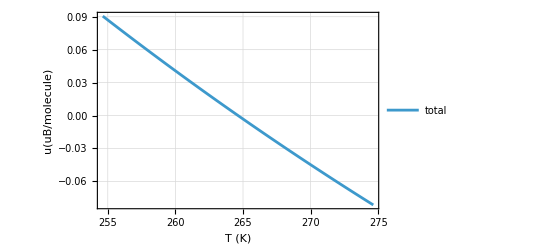

InterpolatingFunction::dmval: Input value {309.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*total moment and magnetization*)
Clear[NA,u,muBSI,mTb,mFe,mO,m03f1,v03f1,m03f1r,v03f1r,mTbIG,ng03f1,MT03f1,M03f1,pur,perovMomenti,iperovMoment,hemMomentt,hemMomentm,hemMomenti,ihemMoment,perovPct,hemPct,mPerov,mHemat,np03f1,nh03f1,tct,Ttreq,lTtreq,s0,BT,d,TC];
(*data*)
NA=6.022*10^23;
u=1.66 10^-27;(*amu, kg*)
muBSI = (1 10^-3)muB;(*Bohr Magneton, J/T*)
mTb = 158.93;(*Tb mass, u*)
mFe = 55.854;(*Fe mass, u*)
mO=15.999;(*O mass, u*)
m03f1=8.598 10^-3;(*sample mass, kg*)
m03f1r=7.973 10^-3;(*revised sample mass, kg*)
v03f1 = 2.118 10^-6;(*sample volume, m^3*)
v03f1r = 2.098 10^-6;(*revised sample volume, m^3*)
pur=0.887;(*purity (% of garnet phase) for 2023 HFIR*)
pur=0.908; (*contaminated powder; comparing to squid data*)
s0=0.039;(*zero-T perovskite moment [Treves1965],uB/molecule*)
BT=0.95;(*pure S=5/2 ferromagnet T-dependence, approx.[Dionne2009]*)
d=0.32;(*Fe-Tb interaction parameter [Treves1965]]*)
TC = 650.;(*perovskite Curie T [Treves1965], K]*)
(*calculations*)
(*perovMoment ={0.075,.072,.070,.067}; (*uB/molecule for perovskite [Park2008], this was ZFC at 300Oe applied field so may not be valid*)*)
(*perovMoment ={0.039,.039,.039,.039}; (*s0 (interpretation 1 of old data) [Treves1965]*)*)
perovMomenti=Table[{i dT,(-s0 BT (1.+d TC/i))},{i,1,Tm}];(*perovskite moment, uB/molecule; convention is negative*)
iperovMoment=Interpolation[perovMomenti];(*interpolated perovskite moment*)
hemMomentt={1.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.,210.,220.,230.,240.,250.,260.,270.,280.,290.,300.};(*hematite moment T data [Andre-Filho2014]]*)
hemMomentm=-(159.69/NA*1.078*10^20){0.019,0.019,0.019,0.019,0.019,0.019,0.0191,0.0192,0.0193,0.0194,0.0195,0.0196,0.0197,0.0198,0.0199,0.02,0.0201,0.0202,0.0205,0.021,0.0215,0.022,0.023,0.025,0.03,0.04,0.06,0.09,.11,.12,.123};(*hematite moment data [Andre-Filho2014],from emu/g to uB/molecule, convention is negative*)
hemMomenti=Table[{hemMomentt[[i]],hemMomentm[[i]]},{i,1,31}];(*hematite moment data [Andre-Filho2014]]*)
ihemMoment=Interpolation[hemMomenti];(*interpolated hematite moment*)
perovPct = .086; 
perovPct=0.072;
hemPct = .027;
hempct=0.020;
mTbIG = 3.0 mTb+5.0 mFe+12.0 mO;(*TbIG mass, u*)
mPerov = mTb + mFe + 3.0 mO;(*perovskite mass, u*)
mHemat = 2.0 mFe + 3.0 mO;(*hematite mass, u*)
ng03f1=pur m03f1r /(u mTbIG);(*molecules of garnet*)
np03f1 = perovPct m03f1r/(u mPerov);(*molecules of perovskite*)
nh03f1 = hemPct m03f1r /(u mHemat); (*molecules of hematite*)
tct=FindRoot[(muBSI ng03f1 imust[T]+muBSI  np03f1 iperovMoment[T]+muBSI  nh03f1 ihemMoment[T])==0.,{T,100.}][[1,2]];(*total TC: compute total moment as function of T, then find root*)
(*Plot*)
mtp=Plot[{(muBSI ng03f1 imust[T]+muBSI  np03f1 iperovMoment[T]+muBSI  nh03f1 ihemMoment[T])/muBSI/ (ng03f1+nh03f1+np03f1)},{T,tct-10.,tct+10.},Frame->True,GridLines->Automatic,FrameLabel->{{"u(uB/molecule)"," "},{"T (K)","Moment vs Temperature"}},PlotLegends->{"total"}, PlotRange->All]
Ttreq={tct-10.,tct,tct+10.,tct+45.};(*revised sample temperatures*)
lTtreq=Length[Ttreq];
MgT03f1=muBSI ng03f1 imust[Ttreq];(*garnet magnetic moment, J/T*)
Mg03f1=MgT03f1/v03f1r;(*garnet magnetization, A/m*)

MT03f1=muBSI ng03f1 imust[Ttreq]+ muBSI np03f1 iperovMoment[Ttreq]+ muBSI nh03f1 ihemMoment[Ttreq];(*sample magnetic moment, J/T*)
M03f1=MT03f1/v03f1r;(*sample magnetization, A/m*)
```

InterpolatingFunction::dmval: Input value {299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

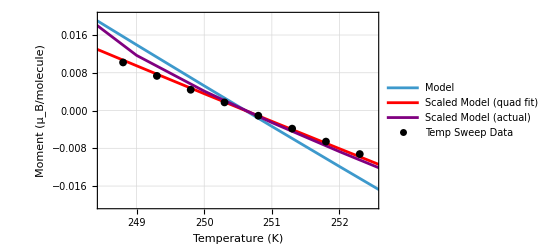

/Users/beckethill/documents/research/NSR/Model vs Data Actual Scalings.png

```mathematica
(*matching the compensation points*)
tcTempSweep=250.9;
tcShift=Round[tcTempSweep]-Round[tct];
shiftedmusti=musti[[200-tcShift;;300-tcShift]]/. {x_,y_}:>{x+tcShift,y};

hemMomentTable=Table[{x,ihemMoment[x]},{x,200,300,1}];
perovMomentTable=Table[{x,iperovMoment[x]},{x,200,300,1}];
garnetMomentTable=Table[{x,imust[x]},{x,200,300,1}];
garnetMomentTable=shiftedmusti;


(*Table of total moments, uB/molecule*)
totalMomentTable=MapThread[{#1[[1]],(muBSI ng03f1 #1[[2]]+muBSI  np03f1#2[[2]]+muBSI  nh03f1#3[[2]])/muBSI/ (ng03f1+nh03f1+np03f1)}&,{garnetMomentTable,perovMomentTable,hemMomentTable}];


(*Scaling factor function; quadratic w/ fixed mean*)
a=-6.9*10^(-5); (*actual scaling factor fit*)
b=0.682;

(*a=-2*10^(-5);(*better scaling factor fit*)
b=0.65;*)

f[x_]:=a(x-tcTempSweep)^2+b;
scalingTable=Table[{x,f[x]},{x,200,300,1}];

(*Exact scaling factors*)
scalings={0.484,0.539,0.57,0.594,0.613,0.628,0.647,0.667,0.693,0.72,0.734,0.759,0.787,0.84,0.994,0.866,0.815,0.8,0.758,0.761,0.711,0.68,0.655,0.634,0.621,0.605,0.589,0.568,0.548};
temps = {300,295,290,285,280,275,270,265,260,255,254,253,252,251,250,249,248,247,246,245,240,235,230,225,220,215,210,205,200}-2;

actualScalingFx=Interpolation[Transpose[{temps,scalings}]];
actualScalingTable=Table[{x,actualScalingFx[x]},{x,200,300,1}];


(*powder temp sweep from 300-200 hysteresis run, March*)
temp={200.0006714,204.8883438,209.8895111,214.8862991,219.89053345,224.8862076,229.8876572,234.88748935,239.9004211,244.88952635,249.88948055,254.88882445,259.88768005,264.88697815,269.88887025,274.88960265,279.8905487,284.88941955,289.8879547,294.88716125,299.8876648};
magub=-{-0.35144431,-0.30852045,-0.2678802,-0.22896352,-0.19191076,-0.15672493,-0.12320405,-0.09163705,-0.06135388,-0.03269348,-0.00539153,0.02069588,0.04569576,0.0696577,0.09260014,0.11448252,0.13533777,0.15481686,0.17321922,0.19027263,0.20632986};

(*small powder temp sweep from 255-245 hysteresis run, 18Apr2025*)
smalltemp={254.86,254.12,253.65,253.1,252.6,252.1,251.6,251.1,250.6,250.1,249.6,249.1,248.6,248.1,247.6,247.1,246.6,246.1,245.6,245.1}+1.7;
smallmagub=-{0.0015,.0013,.001199,.001076,.00095,.00083,.0007,.00057,.00044,.000314,.000183,5.24*10^(-5),-8.21*10^(-5),-.00021,-.00035,-.000486,-.000621,-.000762,-.0009,-.00104}*20.957;
smallscaling={.6,.6,.6,.6,.6,.6};

(*using scale factors on model*)
scaledMoment=MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{totalMomentTable,scalingTable}];
scaledMomentstatic=MapThread[{#1[[1]],#1[[2]]*0.6}&,{totalMomentTable}];
scaledMomentActual=MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{totalMomentTable,actualScalingTable}];

(*Plotting model and scaled model*)
combinedPlot=Show[ListPlot[{totalMomentTable,scaledMoment,scaledMomentActual,Transpose[{smalltemp,smallmagub}]},Joined->{True,True,True,False},PlotMarkers->{None,None,None,{"●",8}},Frame->True,PlotStyle->{Automatic,Red,Purple,Black},FrameLabel->{Style["Temperature (K)",Black,16],Style["Moment (μ_B/molecule)",Black,16]},FrameTicksStyle->Directive[FontSize->12,Black],PlotLegends->Placed[{"Model","Scaled Model (quad fit)","Scaled Model (actual)","Temp Sweep Data"},{0.25,0.25}],PlotStyle->{Thickness[0.005]},GridLines->Automatic,ImageSize->400,BaseStyle->{FontColor->Black},PlotStyle->Black,PlotRange->{{248.5,252.5},{-.02,0.02}}]]

(*combinedPlot=Show[ListPlot[{totalMomentTable,scaledMoment,scaledMomentstatic,Transpose[{temp,magub}]},Joined->{True,True,True,False},PlotMarkers->{None,None,None,{"●",8}},Frame->True,FrameLabel->{Style["Temperature (K)",Black,16],Style["Moment (μ_B/molecule)",Black,16]},FrameTicksStyle->Directive[FontSize->12,Black],PlotLegends->Placed[{"Model","Scaled Model (varied)","Scaled Model (0.6)","Temp Sweep Data"},{0.25,0.25}],PlotStyle->{Thickness[0.005]},GridLines->Automatic,ImageSize->400,BaseStyle->{FontColor->Black},PlotStyle->Black,PlotRange->{{248.5,252.5},{-0.02,0.02}}]]*)


(*combinedPlot=Show[ListPlot[{totalMomentTable,Transpose[{temp,magub}]},Joined->{True,False},PlotMarkers->{None,{"●",8}},Frame->True,FrameLabel->{Style["Temperature (K)",Black,16],Style["Moment (μ_B/molecule)",Black,16]},FrameTicksStyle->Directive[FontSize->12,Black],PlotLegends->Placed[{"Model","Temp Sweep Data"},{0.8,0.85}],PlotStyle->{Thickness[0.005]},GridLines->Automatic,ImageSize->400,BaseStyle->{FontColor->Black},PlotStyle->Black]]*)

(*Export["/Users/beckethill/documents/research/NSR/Model vs Data.png",combinedPlot,ImageResolution->300];*)
(*Export["/Users/beckethill/documents/research/NSR/Model vs Data Scaled.png",combinedPlot,ImageResolution->300]*)
(*Export["/Users/beckethill/documents/research/NSR/Model vs Data Scaled 0.6.png",combinedPlot,ImageResolution->300]*)
(*Export["/Users/beckethill/documents/research/NSR/Adjusted Model vs Data.png",combinedPlot,ImageResolution->300];*)
(*Export["/Users/beckethill/documents/research/NSR/Model vs Data All Scalings.png",combinedPlot,ImageResolution->300]*)
Export["/Users/beckethill/documents/research/NSR/Model vs Data Actual Scalings.png",combinedPlot,ImageResolution->300]
```

1.36561-0.00544786 x

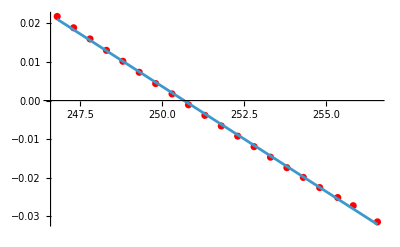

```mathematica
ClearAll[x];
data=Transpose[{smalltemp,smallmagub}];
line=Fit[data,{1,x},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,Min[smalltemp],Max[smalltemp]}]]
```

2.16489-0.0086368 x

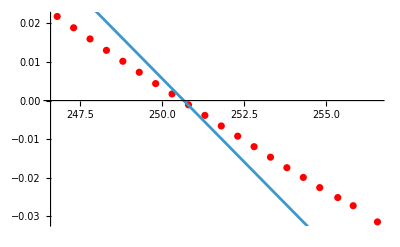

```mathematica
line=Fit[totalMomentTable[[46;;56]],{1,x},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,Min[smalltemp],Max[smalltemp]}]]
```